```mathematica
(*EX1*)
Do[If[Total[Divisors[x]]==2x,Print[x]],{x,100000}]
```

6

28

496

8128

```mathematica
(*或*)
Table[PerfectNumber[x],{x,10}]
```

{6,28,496,8128,33550336,8589869056,137438691328,2305843008139952128,2658455991569831744654692615953842176,191561942608236107294793378084303638130997321548169216}

```mathematica
(*EX2*)
N[Limit[∏_(i=3)^n (1-1/i^2),n->∞],5]
```

0.66667

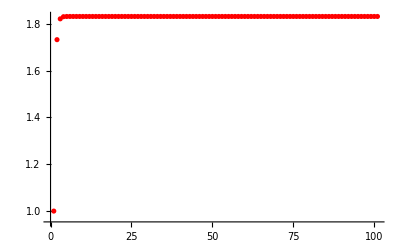

SetDelayed::write: Tag Integer in 1[n_Integer] is Protected.

$Failed

1[1000]

```mathematica
(*EX3*)
F[x_]:=√(2+√x)
ListPlot[NestList[F,1,100],PlotStyle->Red]
G[n_Integer]:=N[Nest[F,1,n],6]
G[1000]
```

```mathematica
(*EX4*)
Q[x_Integer]:=1/x^3
s=0
Do[If[Q[x]>=10^-5,s=s+Q[x],s=s],{x,100}]
Print[N[s]]
```

0

1.20183

```mathematica
(*Ex5*)
r1=∫(x^3+3x^2-5)/((x^2-2x-6)(x^3+x+1))ⅆx
r2=∫Sin[((Cos[x])^2)]*Sin[x]ⅆx
```

((469+248 √7) Log[1+√7-x]+(469-248 √7) Log[-1+√7+x]-14 RootSum[1+#1+#1^3&,(-256 Log[x-#1]+44 Log[x-#1] #1+67 Log[x-#1] #1^2)/(1+3 #1^2)&])/3794

-√(π/2) FresnelS[√(2/π) Cos[x]]

```mathematica
(*EX6*)
n=6(*可选择2-6任意一个数，只要保证与A定义中{Subscript[x, i]}吻合*)
J[j_]:=j
L[i_]:=i
A=Transpose[Table[Table[a^b,{b,0,n-1}],{a,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}]]
re1=∏_(j=2)^n (∏_(i=1)^(j-1) (Subscript[x, J[j]]-Subscript[x, L[i]]))
re2=Det[A]
Simplify[re1-re2]
```

6

{{1,1,1,1,1,1},{x_1,x_2,x_3,x_4,x_5,x_6},{x_1^2,x_2^2,x_3^2,x_4^2,x_5^2,x_6^2},{x_1^3,x_2^3,x_3^3,x_4^3,x_5^3,x_6^3},{x_1^4,x_2^4,x_3^4,x_4^4,x_5^4,x_6^4},{x_1^5,x_2^5,x_3^5,x_4^5,x_5^5,x_6^5}}

(-x_1+x_2) (-x_1+x_3) (-x_2+x_3) (-x_1+x_4) (-x_2+x_4) (-x_3+x_4) (-x_1+x_5) (-x_2+x_5) (-x_3+x_5) (-x_4+x_5) (-x_1+x_6) (-x_2+x_6) (-x_3+x_6) (-x_4+x_6) (-x_5+x_6)

((x_1^3 x_2^2 x_3-x_1^2 x_2^3 x_3-x_1^3 x_2 x_3^2+x_1 x_2^3 x_3^2+x_1^2 x_2 x_3^3-x_1 x_2^2 x_3^3-x_1^3 x_2^2 x_4+x_1^2 x_2^3 x_4+x_1^3 x_3^2 x_4-x_2^3 x_3^2 x_4-x_1^2 x_3^3 x_4+x_2^2 x_3^3 x_4+x_1^3 x_2 x_4^2-x_1 x_2^3 x_4^2-x_1^3 x_3 x_4^2+x_2^3 x_3 x_4^2+x_1 x_3^3 x_4^2-x_2 x_3^3 x_4^2-x_1^2 x_2 x_4^3+x_1 x_2^2 x_4^3+x_1^2 x_3 x_4^3-x_2^2 x_3 x_4^3-x_1 x_3^2 x_4^3+x_2 x_3^2 x_4^3) x_5^4-x_4^4 (x_1^3 x_2^2 x_3-x_1^2 x_2^3 x_3-x_1^3 x_2 x_3^2+x_1 x_2^3 x_3^2+x_1^2 x_2 x_3^3-x_1 x_2^2 x_3^3-x_1^3 x_2^2 x_5+x_1^2 x_2^3 x_5+x_1^3 x_3^2 x_5-x_2^3 x_3^2 x_5-x_1^2 x_3^3 x_5+x_2^2 x_3^3 x_5+x_1^3 x_2 x_5^2-x_1 x_2^3 x_5^2-x_1^3 x_3 x_5^2+x_2^3 x_3 x_5^2+x_1 x_3^3 x_5^2-x_2 x_3^3 x_5^2-x_1^2 x_2 x_5^3+x_1 x_2^2 x_5^3+x_1^2 x_3 x_5^3-x_2^2 x_3 x_5^3-x_1 x_3^2 x_5^3+x_2 x_3^2 x_5^3)+x_3^4 (x_1^3 x_2^2 x_4-x_1^2 x_2^3 x_4-x_1^3 x_2 x_4^2+x_1 x_2^3 x_4^2+x_1^2 x_2 x_4^3-x_1 x_2^2 x_4^3-x_1^3 x_2^2 x_5+x_1^2 x_2^3 x_5+x_1^3 x_4^2 x_5-x_2^3 x_4^2 x_5-x_1^2 x_4^3 x_5+x_2^2 x_4^3 x_5+x_1^3 x_2 x_5^2-x_1 x_2^3 x_5^2-x_1^3 x_4 x_5^2+x_2^3 x_4 x_5^2+x_1 x_4^3 x_5^2-x_2 x_4^3 x_5^2-x_1^2 x_2 x_5^3+x_1 x_2^2 x_5^3+x_1^2 x_4 x_5^3-x_2^2 x_4 x_5^3-x_1 x_4^2 x_5^3+x_2 x_4^2 x_5^3)-x_2^4 (x_1^3 x_3^2 x_4-x_1^2 x_3^3 x_4-x_1^3 x_3 x_4^2+x_1 x_3^3 x_4^2+x_1^2 x_3 x_4^3-x_1 x_3^2 x_4^3-x_1^3 x_3^2 x_5+x_1^2 x_3^3 x_5+x_1^3 x_4^2 x_5-x_3^3 x_4^2 x_5-x_1^2 x_4^3 x_5+x_3^2 x_4^3 x_5+x_1^3 x_3 x_5^2-x_1 x_3^3 x_5^2-x_1^3 x_4 x_5^2+x_3^3 x_4 x_5^2+x_1 x_4^3 x_5^2-x_3 x_4^3 x_5^2-x_1^2 x_3 x_5^3+x_1 x_3^2 x_5^3+x_1^2 x_4 x_5^3-x_3^2 x_4 x_5^3-x_1 x_4^2 x_5^3+x_3 x_4^2 x_5^3)+x_1^4 (x_2^3 x_3^2 x_4-x_2^2 x_3^3 x_4-x_2^3 x_3 x_4^2+x_2 x_3^3 x_4^2+x_2^2 x_3 x_4^3-x_2 x_3^2 x_4^3-x_2^3 x_3^2 x_5+x_2^2 x_3^3 x_5+x_2^3 x_4^2 x_5-x_3^3 x_4^2 x_5-x_2^2 x_4^3 x_5+x_3^2 x_4^3 x_5+x_2^3 x_3 x_5^2-x_2 x_3^3 x_5^2-x_2^3 x_4 x_5^2+x_3^3 x_4 x_5^2+x_2 x_4^3 x_5^2-x_3 x_4^3 x_5^2-x_2^2 x_3 x_5^3+x_2 x_3^2 x_5^3+x_2^2 x_4 x_5^3-x_3^2 x_4 x_5^3-x_2 x_4^2 x_5^3+x_3 x_4^2 x_5^3)) x_6^5-x_5^5 ((x_1^3 x_2^2 x_3-x_1^2 x_2^3 x_3-x_1^3 x_2 x_3^2+x_1 x_2^3 x_3^2+x_1^2 x_2 x_3^3-x_1 x_2^2 x_3^3-x_1^3 x_2^2 x_4+x_1^2 x_2^3 x_4+x_1^3 x_3^2 x_4-x_2^3 x_3^2 x_4-x_1^2 x_3^3 x_4+x_2^2 x_3^3 x_4+x_1^3 x_2 x_4^2-x_1 x_2^3 x_4^2-x_1^3 x_3 x_4^2+x_2^3 x_3 x_4^2+x_1 x_3^3 x_4^2-x_2 x_3^3 x_4^2-x_1^2 x_2 x_4^3+x_1 x_2^2 x_4^3+x_1^2 x_3 x_4^3-x_2^2 x_3 x_4^3-x_1 x_3^2 x_4^3+x_2 x_3^2 x_4^3) x_6^4-x_4^4 (x_1^3 x_2^2 x_3-x_1^2 x_2^3 x_3-x_1^3 x_2 x_3^2+x_1 x_2^3 x_3^2+x_1^2 x_2 x_3^3-x_1 x_2^2 x_3^3-x_1^3 x_2^2 x_6+x_1^2 x_2^3 x_6+x_1^3 x_3^2 x_6-x_2^3 x_3^2 x_6-x_1^2 x_3^3 x_6+x_2^2 x_3^3 x_6+x_1^3 x_2 x_6^2-x_1 x_2^3 x_6^2-x_1^3 x_3 x_6^2+x_2^3 x_3 x_6^2+x_1 x_3^3 x_6^2-x_2 x_3^3 x_6^2-x_1^2 x_2 x_6^3+x_1 x_2^2 x_6^3+x_1^2 x_3 x_6^3-x_2^2 x_3 x_6^3-x_1 x_3^2 x_6^3+x_2 x_3^2 x_6^3)+x_3^4 (x_1^3 x_2^2 x_4-x_1^2 x_2^3 x_4-x_1^3 x_2 x_4^2+x_1 x_2^3 x_4^2+x_1^2 x_2 x_4^3-x_1 x_2^2 x_4^3-x_1^3 x_2^2 x_6+x_1^2 x_2^3 x_6+x_1^3 x_4^2 x_6-x_2^3 x_4^2 x_6-x_1^2 x_4^3 x_6+x_2^2 x_4^3 x_6+x_1^3 x_2 x_6^2-x_1 x_2^3 x_6^2-x_1^3 x_4 x_6^2+x_2^3 x_4 x_6^2+x_1 x_4^3 x_6^2-x_2 x_4^3 x_6^2-x_1^2 x_2 x_6^3+x_1 x_2^2 x_6^3+x_1^2 x_4 x_6^3-x_2^2 x_4 x_6^3-x_1 x_4^2 x_6^3+x_2 x_4^2 x_6^3)-x_2^4 (x_1^3 x_3^2 x_4-x_1^2 x_3^3 x_4-x_1^3 x_3 x_4^2+x_1 x_3^3 x_4^2+x_1^2 x_3 x_4^3-x_1 x_3^2 x_4^3-x_1^3 x_3^2 x_6+x_1^2 x_3^3 x_6+x_1^3 x_4^2 x_6-x_3^3 x_4^2 x_6-x_1^2 x_4^3 x_6+x_3^2 x_4^3 x_6+x_1^3 x_3 x_6^2-x_1 x_3^3 x_6^2-x_1^3 x_4 x_6^2+x_3^3 x_4 x_6^2+x_1 x_4^3 x_6^2-x_3 x_4^3 x_6^2-x_1^2 x_3 x_6^3+x_1 x_3^2 x_6^3+x_1^2 x_4 x_6^3-x_3^2 x_4 x_6^3-x_1 x_4^2 x_6^3+x_3 x_4^2 x_6^3)+x_1^4 (x_2^3 x_3^2 x_4-x_2^2 x_3^3 x_4-x_2^3 x_3 x_4^2+x_2 x_3^3 x_4^2+x_2^2 x_3 x_4^3-x_2 x_3^2 x_4^3-x_2^3 x_3^2 x_6+x_2^2 x_3^3 x_6+x_2^3 x_4^2 x_6-x_3^3 x_4^2 x_6-x_2^2 x_4^3 x_6+x_3^2 x_4^3 x_6+x_2^3 x_3 x_6^2-x_2 x_3^3 x_6^2-x_2^3 x_4 x_6^2+x_3^3 x_4 x_6^2+x_2 x_4^3 x_6^2-x_3 x_4^3 x_6^2-x_2^2 x_3 x_6^3+x_2 x_3^2 x_6^3+x_2^2 x_4 x_6^3-x_3^2 x_4 x_6^3-x_2 x_4^2 x_6^3+x_3 x_4^2 x_6^3))+x_4^5 ((x_1^3 x_2^2 x_3-x_1^2 x_2^3 x_3-x_1^3 x_2 x_3^2+x_1 x_2^3 x_3^2+x_1^2 x_2 x_3^3-x_1 x_2^2 x_3^3-x_1^3 x_2^2 x_5+x_1^2 x_2^3 x_5+x_1^3 x_3^2 x_5-x_2^3 x_3^2 x_5-x_1^2 x_3^3 x_5+x_2^2 x_3^3 x_5+x_1^3 x_2 x_5^2-x_1 x_2^3 x_5^2-x_1^3 x_3 x_5^2+x_2^3 x_3 x_5^2+x_1 x_3^3 x_5^2-x_2 x_3^3 x_5^2-x_1^2 x_2 x_5^3+x_1 x_2^2 x_5^3+x_1^2 x_3 x_5^3-x_2^2 x_3 x_5^3-x_1 x_3^2 x_5^3+x_2 x_3^2 x_5^3) x_6^4-x_5^4 (x_1^3 x_2^2 x_3-x_1^2 x_2^3 x_3-x_1^3 x_2 x_3^2+x_1 x_2^3 x_3^2+x_1^2 x_2 x_3^3-x_1 x_2^2 x_3^3-x_1^3 x_2^2 x_6+x_1^2 x_2^3 x_6+x_1^3 x_3^2 x_6-x_2^3 x_3^2 x_6-x_1^2 x_3^3 x_6+x_2^2 x_3^3 x_6+x_1^3 x_2 x_6^2-x_1 x_2^3 x_6^2-x_1^3 x_3 x_6^2+x_2^3 x_3 x_6^2+x_1 x_3^3 x_6^2-x_2 x_3^3 x_6^2-x_1^2 x_2 x_6^3+x_1 x_2^2 x_6^3+x_1^2 x_3 x_6^3-x_2^2 x_3 x_6^3-x_1 x_3^2 x_6^3+x_2 x_3^2 x_6^3)+x_3^4 (x_1^3 x_2^2 x_5-x_1^2 x_2^3 x_5-x_1^3 x_2 x_5^2+x_1 x_2^3 x_5^2+x_1^2 x_2 x_5^3-x_1 x_2^2 x_5^3-x_1^3 x_2^2 x_6+x_1^2 x_2^3 x_6+x_1^3 x_5^2 x_6-x_2^3 x_5^2 x_6-x_1^2 x_5^3 x_6+x_2^2 x_5^3 x_6+x_1^3 x_2 x_6^2-x_1 x_2^3 x_6^2-x_1^3 x_5 x_6^2+x_2^3 x_5 x_6^2+x_1 x_5^3 x_6^2-x_2 x_5^3 x_6^2-x_1^2 x_2 x_6^3+x_1 x_2^2 x_6^3+x_1^2 x_5 x_6^3-x_2^2 x_5 x_6^3-x_1 x_5^2 x_6^3+x_2 x_5^2 x_6^3)-x_2^4 (x_1^3 x_3^2 x_5-x_1^2 x_3^3 x_5-x_1^3 x_3 x_5^2+x_1 x_3^3 x_5^2+x_1^2 x_3 x_5^3-x_1 x_3^2 x_5^3-x_1^3 x_3^2 x_6+x_1^2 x_3^3 x_6+x_1^3 x_5^2 x_6-x_3^3 x_5^2 x_6-x_1^2 x_5^3 x_6+x_3^2 x_5^3 x_6+x_1^3 x_3 x_6^2-x_1 x_3^3 x_6^2-x_1^3 x_5 x_6^2+x_3^3 x_5 x_6^2+x_1 x_5^3 x_6^2-x_3 x_5^3 x_6^2-x_1^2 x_3 x_6^3+x_1 x_3^2 x_6^3+x_1^2 x_5 x_6^3-x_3^2 x_5 x_6^3-x_1 x_5^2 x_6^3+x_3 x_5^2 x_6^3)+x_1^4 (x_2^3 x_3^2 x_5-x_2^2 x_3^3 x_5-x_2^3 x_3 x_5^2+x_2 x_3^3 x_5^2+x_2^2 x_3 x_5^3-x_2 x_3^2 x_5^3-x_2^3 x_3^2 x_6+x_2^2 x_3^3 x_6+x_2^3 x_5^2 x_6-x_3^3 x_5^2 x_6-x_2^2 x_5^3 x_6+x_3^2 x_5^3 x_6+x_2^3 x_3 x_6^2-x_2 x_3^3 x_6^2-x_2^3 x_5 x_6^2+x_3^3 x_5 x_6^2+x_2 x_5^3 x_6^2-x_3 x_5^3 x_6^2-x_2^2 x_3 x_6^3+x_2 x_3^2 x_6^3+x_2^2 x_5 x_6^3-x_3^2 x_5 x_6^3-x_2 x_5^2 x_6^3+x_3 x_5^2 x_6^3))-x_3^5 ((x_1^3 x_2^2 x_4-x_1^2 x_2^3 x_4-x_1^3 x_2 x_4^2+x_1 x_2^3 x_4^2+x_1^2 x_2 x_4^3-x_1 x_2^2 x_4^3-x_1^3 x_2^2 x_5+x_1^2 x_2^3 x_5+x_1^3 x_4^2 x_5-x_2^3 x_4^2 x_5-x_1^2 x_4^3 x_5+x_2^2 x_4^3 x_5+x_1^3 x_2 x_5^2-x_1 x_2^3 x_5^2-x_1^3 x_4 x_5^2+x_2^3 x_4 x_5^2+x_1 x_4^3 x_5^2-x_2 x_4^3 x_5^2-x_1^2 x_2 x_5^3+x_1 x_2^2 x_5^3+x_1^2 x_4 x_5^3-x_2^2 x_4 x_5^3-x_1 x_4^2 x_5^3+x_2 x_4^2 x_5^3) x_6^4-x_5^4 (x_1^3 x_2^2 x_4-x_1^2 x_2^3 x_4-x_1^3 x_2 x_4^2+x_1 x_2^3 x_4^2+x_1^2 x_2 x_4^3-x_1 x_2^2 x_4^3-x_1^3 x_2^2 x_6+x_1^2 x_2^3 x_6+x_1^3 x_4^2 x_6-x_2^3 x_4^2 x_6-x_1^2 x_4^3 x_6+x_2^2 x_4^3 x_6+x_1^3 x_2 x_6^2-x_1 x_2^3 x_6^2-x_1^3 x_4 x_6^2+x_2^3 x_4 x_6^2+x_1 x_4^3 x_6^2-x_2 x_4^3 x_6^2-x_1^2 x_2 x_6^3+x_1 x_2^2 x_6^3+x_1^2 x_4 x_6^3-x_2^2 x_4 x_6^3-x_1 x_4^2 x_6^3+x_2 x_4^2 x_6^3)+x_4^4 (x_1^3 x_2^2 x_5-x_1^2 x_2^3 x_5-x_1^3 x_2 x_5^2+x_1 x_2^3 x_5^2+x_1^2 x_2 x_5^3-x_1 x_2^2 x_5^3-x_1^3 x_2^2 x_6+x_1^2 x_2^3 x_6+x_1^3 x_5^2 x_6-x_2^3 x_5^2 x_6-x_1^2 x_5^3 x_6+x_2^2 x_5^3 x_6+x_1^3 x_2 x_6^2-x_1 x_2^3 x_6^2-x_1^3 x_5 x_6^2+x_2^3 x_5 x_6^2+x_1 x_5^3 x_6^2-x_2 x_5^3 x_6^2-x_1^2 x_2 x_6^3+x_1 x_2^2 x_6^3+x_1^2 x_5 x_6^3-x_2^2 x_5 x_6^3-x_1 x_5^2 x_6^3+x_2 x_5^2 x_6^3)-x_2^4 (x_1^3 x_4^2 x_5-x_1^2 x_4^3 x_5-x_1^3 x_4 x_5^2+x_1 x_4^3 x_5^2+x_1^2 x_4 x_5^3-x_1 x_4^2 x_5^3-x_1^3 x_4^2 x_6+x_1^2 x_4^3 x_6+x_1^3 x_5^2 x_6-x_4^3 x_5^2 x_6-x_1^2 x_5^3 x_6+x_4^2 x_5^3 x_6+x_1^3 x_4 x_6^2-x_1 x_4^3 x_6^2-x_1^3 x_5 x_6^2+x_4^3 x_5 x_6^2+x_1 x_5^3 x_6^2-x_4 x_5^3 x_6^2-x_1^2 x_4 x_6^3+x_1 x_4^2 x_6^3+x_1^2 x_5 x_6^3-x_4^2 x_5 x_6^3-x_1 x_5^2 x_6^3+x_4 x_5^2 x_6^3)+x_1^4 (x_2^3 x_4^2 x_5-x_2^2 x_4^3 x_5-x_2^3 x_4 x_5^2+x_2 x_4^3 x_5^2+x_2^2 x_4 x_5^3-x_2 x_4^2 x_5^3-x_2^3 x_4^2 x_6+x_2^2 x_4^3 x_6+x_2^3 x_5^2 x_6-x_4^3 x_5^2 x_6-x_2^2 x_5^3 x_6+x_4^2 x_5^3 x_6+x_2^3 x_4 x_6^2-x_2 x_4^3 x_6^2-x_2^3 x_5 x_6^2+x_4^3 x_5 x_6^2+x_2 x_5^3 x_6^2-x_4 x_5^3 x_6^2-x_2^2 x_4 x_6^3+x_2 x_4^2 x_6^3+x_2^2 x_5 x_6^3-x_4^2 x_5 x_6^3-x_2 x_5^2 x_6^3+x_4 x_5^2 x_6^3))+x_2^5 ((x_1^3 x_3^2 x_4-x_1^2 x_3^3 x_4-x_1^3 x_3 x_4^2+x_1 x_3^3 x_4^2+x_1^2 x_3 x_4^3-x_1 x_3^2 x_4^3-x_1^3 x_3^2 x_5+x_1^2 x_3^3 x_5+x_1^3 x_4^2 x_5-x_3^3 x_4^2 x_5-x_1^2 x_4^3 x_5+x_3^2 x_4^3 x_5+x_1^3 x_3 x_5^2-x_1 x_3^3 x_5^2-x_1^3 x_4 x_5^2+x_3^3 x_4 x_5^2+x_1 x_4^3 x_5^2-x_3 x_4^3 x_5^2-x_1^2 x_3 x_5^3+x_1 x_3^2 x_5^3+x_1^2 x_4 x_5^3-x_3^2 x_4 x_5^3-x_1 x_4^2 x_5^3+x_3 x_4^2 x_5^3) x_6^4-x_5^4 (x_1^3 x_3^2 x_4-x_1^2 x_3^3 x_4-x_1^3 x_3 x_4^2+x_1 x_3^3 x_4^2+x_1^2 x_3 x_4^3-x_1 x_3^2 x_4^3-x_1^3 x_3^2 x_6+x_1^2 x_3^3 x_6+x_1^3 x_4^2 x_6-x_3^3 x_4^2 x_6-x_1^2 x_4^3 x_6+x_3^2 x_4^3 x_6+x_1^3 x_3 x_6^2-x_1 x_3^3 x_6^2-x_1^3 x_4 x_6^2+x_3^3 x_4 x_6^2+x_1 x_4^3 x_6^2-x_3 x_4^3 x_6^2-x_1^2 x_3 x_6^3+x_1 x_3^2 x_6^3+x_1^2 x_4 x_6^3-x_3^2 x_4 x_6^3-x_1 x_4^2 x_6^3+x_3 x_4^2 x_6^3)+x_4^4 (x_1^3 x_3^2 x_5-x_1^2 x_3^3 x_5-x_1^3 x_3 x_5^2+x_1 x_3^3 x_5^2+x_1^2 x_3 x_5^3-x_1 x_3^2 x_5^3-x_1^3 x_3^2 x_6+x_1^2 x_3^3 x_6+x_1^3 x_5^2 x_6-x_3^3 x_5^2 x_6-x_1^2 x_5^3 x_6+x_3^2 x_5^3 x_6+x_1^3 x_3 x_6^2-x_1 x_3^3 x_6^2-x_1^3 x_5 x_6^2+x_3^3 x_5 x_6^2+x_1 x_5^3 x_6^2-x_3 x_5^3 x_6^2-x_1^2 x_3 x_6^3+x_1 x_3^2 x_6^3+x_1^2 x_5 x_6^3-x_3^2 x_5 x_6^3-x_1 x_5^2 x_6^3+x_3 x_5^2 x_6^3)-x_3^4 (x_1^3 x_4^2 x_5-x_1^2 x_4^3 x_5-x_1^3 x_4 x_5^2+x_1 x_4^3 x_5^2+x_1^2 x_4 x_5^3-x_1 x_4^2 x_5^3-x_1^3 x_4^2 x_6+x_1^2 x_4^3 x_6+x_1^3 x_5^2 x_6-x_4^3 x_5^2 x_6-x_1^2 x_5^3 x_6+x_4^2 x_5^3 x_6+x_1^3 x_4 x_6^2-x_1 x_4^3 x_6^2-x_1^3 x_5 x_6^2+x_4^3 x_5 x_6^2+x_1 x_5^3 x_6^2-x_4 x_5^3 x_6^2-x_1^2 x_4 x_6^3+x_1 x_4^2 x_6^3+x_1^2 x_5 x_6^3-x_4^2 x_5 x_6^3-x_1 x_5^2 x_6^3+x_4 x_5^2 x_6^3)+x_1^4 (x_3^3 x_4^2 x_5-x_3^2 x_4^3 x_5-x_3^3 x_4 x_5^2+x_3 x_4^3 x_5^2+x_3^2 x_4 x_5^3-x_3 x_4^2 x_5^3-x_3^3 x_4^2 x_6+x_3^2 x_4^3 x_6+x_3^3 x_5^2 x_6-x_4^3 x_5^2 x_6-x_3^2 x_5^3 x_6+x_4^2 x_5^3 x_6+x_3^3 x_4 x_6^2-x_3 x_4^3 x_6^2-x_3^3 x_5 x_6^2+x_4^3 x_5 x_6^2+x_3 x_5^3 x_6^2-x_4 x_5^3 x_6^2-x_3^2 x_4 x_6^3+x_3 x_4^2 x_6^3+x_3^2 x_5 x_6^3-x_4^2 x_5 x_6^3-x_3 x_5^2 x_6^3+x_4 x_5^2 x_6^3))-x_1^5 ((x_2^3 x_3^2 x_4-x_2^2 x_3^3 x_4-x_2^3 x_3 x_4^2+x_2 x_3^3 x_4^2+x_2^2 x_3 x_4^3-x_2 x_3^2 x_4^3-x_2^3 x_3^2 x_5+x_2^2 x_3^3 x_5+x_2^3 x_4^2 x_5-x_3^3 x_4^2 x_5-x_2^2 x_4^3 x_5+x_3^2 x_4^3 x_5+x_2^3 x_3 x_5^2-x_2 x_3^3 x_5^2-x_2^3 x_4 x_5^2+x_3^3 x_4 x_5^2+x_2 x_4^3 x_5^2-x_3 x_4^3 x_5^2-x_2^2 x_3 x_5^3+x_2 x_3^2 x_5^3+x_2^2 x_4 x_5^3-x_3^2 x_4 x_5^3-x_2 x_4^2 x_5^3+x_3 x_4^2 x_5^3) x_6^4-x_5^4 (x_2^3 x_3^2 x_4-x_2^2 x_3^3 x_4-x_2^3 x_3 x_4^2+x_2 x_3^3 x_4^2+x_2^2 x_3 x_4^3-x_2 x_3^2 x_4^3-x_2^3 x_3^2 x_6+x_2^2 x_3^3 x_6+x_2^3 x_4^2 x_6-x_3^3 x_4^2 x_6-x_2^2 x_4^3 x_6+x_3^2 x_4^3 x_6+x_2^3 x_3 x_6^2-x_2 x_3^3 x_6^2-x_2^3 x_4 x_6^2+x_3^3 x_4 x_6^2+x_2 x_4^3 x_6^2-x_3 x_4^3 x_6^2-x_2^2 x_3 x_6^3+x_2 x_3^2 x_6^3+x_2^2 x_4 x_6^3-x_3^2 x_4 x_6^3-x_2 x_4^2 x_6^3+x_3 x_4^2 x_6^3)+x_4^4 (x_2^3 x_3^2 x_5-x_2^2 x_3^3 x_5-x_2^3 x_3 x_5^2+x_2 x_3^3 x_5^2+x_2^2 x_3 x_5^3-x_2 x_3^2 x_5^3-x_2^3 x_3^2 x_6+x_2^2 x_3^3 x_6+x_2^3 x_5^2 x_6-x_3^3 x_5^2 x_6-x_2^2 x_5^3 x_6+x_3^2 x_5^3 x_6+x_2^3 x_3 x_6^2-x_2 x_3^3 x_6^2-x_2^3 x_5 x_6^2+x_3^3 x_5 x_6^2+x_2 x_5^3 x_6^2-x_3 x_5^3 x_6^2-x_2^2 x_3 x_6^3+x_2 x_3^2 x_6^3+x_2^2 x_5 x_6^3-x_3^2 x_5 x_6^3-x_2 x_5^2 x_6^3+x_3 x_5^2 x_6^3)-x_3^4 (x_2^3 x_4^2 x_5-x_2^2 x_4^3 x_5-x_2^3 x_4 x_5^2+x_2 x_4^3 x_5^2+x_2^2 x_4 x_5^3-x_2 x_4^2 x_5^3-x_2^3 x_4^2 x_6+x_2^2 x_4^3 x_6+x_2^3 x_5^2 x_6-x_4^3 x_5^2 x_6-x_2^2 x_5^3 x_6+x_4^2 x_5^3 x_6+x_2^3 x_4 x_6^2-x_2 x_4^3 x_6^2-x_2^3 x_5 x_6^2+x_4^3 x_5 x_6^2+x_2 x_5^3 x_6^2-x_4 x_5^3 x_6^2-x_2^2 x_4 x_6^3+x_2 x_4^2 x_6^3+x_2^2 x_5 x_6^3-x_4^2 x_5 x_6^3-x_2 x_5^2 x_6^3+x_4 x_5^2 x_6^3)+x_2^4 (x_3^3 x_4^2 x_5-x_3^2 x_4^3 x_5-x_3^3 x_4 x_5^2+x_3 x_4^3 x_5^2+x_3^2 x_4 x_5^3-x_3 x_4^2 x_5^3-x_3^3 x_4^2 x_6+x_3^2 x_4^3 x_6+x_3^3 x_5^2 x_6-x_4^3 x_5^2 x_6-x_3^2 x_5^3 x_6+x_4^2 x_5^3 x_6+x_3^3 x_4 x_6^2-x_3 x_4^3 x_6^2-x_3^3 x_5 x_6^2+x_4^3 x_5 x_6^2+x_3 x_5^3 x_6^2-x_4 x_5^3 x_6^2-x_3^2 x_4 x_6^3+x_3 x_4^2 x_6^3+x_3^2 x_5 x_6^3-x_4^2 x_5 x_6^3-x_3 x_5^2 x_6^3+x_4 x_5^2 x_6^3))

0

```mathematica
(*EX7*)
```

```mathematica
(*EX8*)
A={{1,1,1},{1,2,3},{1,3,2}}
(*任意设，与B中一致*)
s=Eigensystem[A]
B={Normalize[s[[2]][[1]]],Normalize[s[[2]][[2]]],Normalize[s[[2]][[3]]]};
Q=Transpose[B];
d[A_]:=(Inverse[Q]).A.Q
Simplify[d[A]]
```

{{1,1,1},{1,2,3},{1,3,2}}

{{3+√6,-1,3-√6},{{-2+√6,1,1},{0,-1,1},{-2-√6,1,1}}}

{{3+√6,0,0},{0,-1,0},{0,0,3-√6}}

```mathematica
MatrixForm[{{3+√6,0,0},{0,-1,0},{0,0,3-√6}}]
```

(3+√6 | 0 | 0
0 | -1 | 0
0 | 0 | 3-√6)

```mathematica
(*EX9*)
w[x_]:=x-1
q[x_]:=x+1
A={{},{},{}}
```

{{},{},{}}

```mathematica
(*Ex10*)

(*函数1*)
rank1[A_]:=MatrixRank[A]
(*举例*)
A={{1,2,3},{2,4,6},{1,2,1}}
rank1[A]

(*函数2*)
rank2[A_]:=Dimensions[B][[2]]-Dimensions[NullSpace[A]][[1]]
(*举例*)
A={{1,2,3},{2,4,6},{1,2,1}}
rank2[A]
```

{{1,2,3},{2,4,6},{1,2,1}}

2

{{1,2,3},{2,4,6},{1,2,1}}

2

```mathematica
(*EX11*)
A=Table[Table[(i-j)^2,{j,1,20}],{i,1,25}];
NullSpace[A]
```

{{-153,323,-171,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-136,288,-153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{-120,255,-136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{-105,224,-120,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{-91,195,-105,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-78,168,-91,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{-66,143,-78,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{-55,120,-66,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{-45,99,-55,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{-36,80,-45,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-28,63,-36,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{-21,48,-28,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{-15,35,-21,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{-10,24,-15,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{-6,15,-10,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3,8,-6,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,3,-3,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*EX12*)

(*n=10*)
n=10
NSolve[E^x-x^n==0,x,Reals]
(*n=15*)
n=15
NSolve[E^x-x^n==0,x,Reals]
(*n=20*)
n=20
NSolve[E^x-x^n==0,x,Reals]
(*f(x)最大值点及图像*)
f[x_,m_]:=x^m/E^x;
NMaxValue[f[x,3],x](*m可以取其他值*)
ArgMax[f[x,3],x]
```

10

{{x→-0.912765},{x→1.11833},{x→35.7715}}

15

{{x→1.07424},{x→61.8773}}

20

{{x→-0.953446},{x→1.05412},{x→89.9951}}

1.34425

3

1

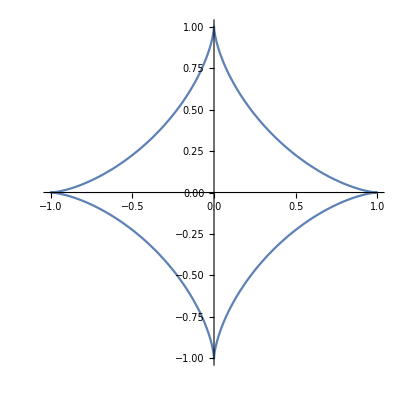

1.1781

```mathematica
(*EX13*)
a=1
ParametricPlot[{a(Cos[t])^3,a(Sin[t])^3},{t,0,2Pi}]
S=4∫_0^(0.5Pi) (a (Sin[t])^3 )*(3a(Cos[t])^2)*Sin[t]ⅆt
```

```mathematica
(*EX14*)
Refine[z[x_,y_]:=x+I*y,x∈Reals&&y∈Reals]
```

```mathematica
(*实部图像*)
Plot3D[N[Re[ArcSin[z[x,y]]],5],{x,0,10},{y,0,10},AxesOrigin->{0,0,0},Lighting->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*虚部图像*)
Plot3D[N[Im[ArcSin[z[x,y]]],5],{x,0,10},{y,0,10},AxesOrigin->{0,0,0},Lighting->Automatic]
```

-Graphics3D-

3

{x^6,6 x^5,30 x^4,120 x^3}

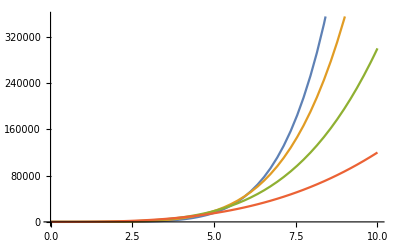

```mathematica
(*EX15*)
d[f_]:=D[f,x];
n=3(*可以换成其他值*)
f[x_]:=x^6(*可以为其他函数*)
b1=NestList[d,f[x],n]
Plot[b1,{x,0,10}]
```

9000000000

1

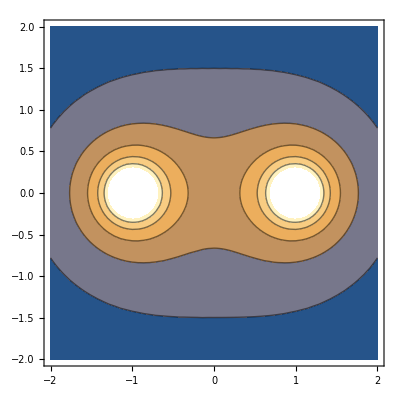

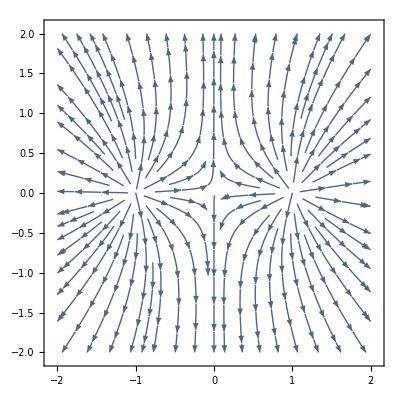

```mathematica
(*EX16*)
(*不妨设两根导线电流大小相等*)
k=9*10^9
Q=1(*具体值可以改变*)

(*电势图*)
ϕ[x_,y_]:=k Q(1/(√((x+1)^2+y^2))+1/(√((x-1)^2+y^2)))
ContourPlot[ϕ[x,y],{x,-2,2},{y,-2,2},Axes->True]

(*电场图*)
e[x_,y_]:={ (k Q*(x-1))/(((x-1)^2+y^2)^1.5)+(k Q*(x+1))/(((x+1)^2+y^2)^1.5),(k Q*y)/(((x+1)^2+y^2)^1.5)+(k Q*y)/(((x-1)^2+y^2)^1.5)}
StreamPlot[e[x,y],{x,-2,2},{y,-2,2}]
```

1/1000000

1/500000

3/1000000

10000

3/5000000

2000

5/3 π Sin[x]

5 π Sin[x]

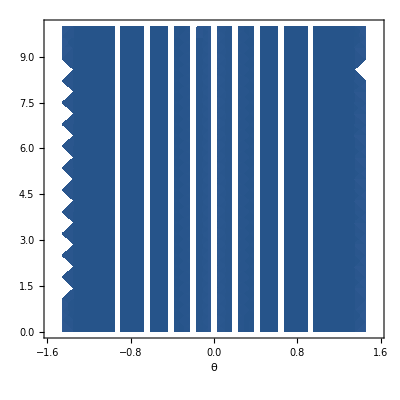

```mathematica
(*EX17*)
a=1*10^-6
b=2*10^-6
d=a+b
n=10000
λ=600*10^-9
Subscript[I, 0]=2000
α=(Pi*a*Sin[x])/λ
β=(Pi*d*Sin[x])/λ
i[x_]:=Subscript[I, 0]*((Sin[(Pi*a*Sin[x])/λ]/((Pi*a*Sin[x])/λ))^2)*((Sin[n*(Pi*d*Sin[x])/λ]/Sin[(Pi*d*Sin[x])/λ])^2)
l[y_]:=1
DensityPlot[i[x]*l[y],{x,-0.5Pi,0.5Pi},{y,0,10},Axes->True,AxesLabel->{θ,None}]
```

```mathematica
(*EX18*)
r=Dynamic[Clock[{0,1},20]]
Show[Graphics[{Dynamic[Hue[Clock[{0,1},20]]],Disk[{0,0},r]}],PlotRange->2]
```

-Graphics-

```mathematica
(*EX19*)
z[x_,y_]:=x^3+y^3-6x y
Solve[z[x,y]==0,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→(2 2^(1/3) x)/((-x^3+√(-32 x^3+x^6))^(1/3))+((-x^3+√(-32 x^3+x^6))^(1/3))/2^(1/3)},{y→-(2^(1/3) (1+ⅈ √3) x)/((-x^3+√(-32 x^3+x^6))^(1/3))-((1-ⅈ √3) (-x^3+√(-32 x^3+x^6))^(1/3))/(2 2^(1/3))},{y→-(2^(1/3) (1-ⅈ √3) x)/((-x^3+√(-32 x^3+x^6))^(1/3))-((1+ⅈ √3) (-x^3+√(-32 x^3+x^6))^(1/3))/(2 2^(1/3))}}

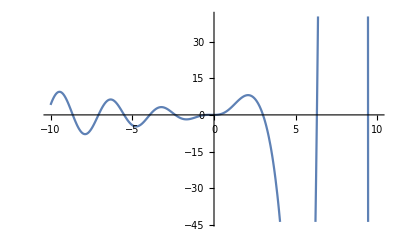

```mathematica
(*20*)
Plot[(E^x)*Sin[x]-x*Cos[2x],{x,-10,10}]
```

```mathematica
N[Reduce[(E^x)*Sin[x]-x*Cos[2x]==0&&-5<x<5,x],5]
```

x==-3.9288||x==-2.3699||x==-0.4561||x==0||x==2.9977

```mathematica
(*EX21*)
Series[∫(1+x)/(4+3x^4+x^6)ⅆx,{x,0,2}]
```

1/6 RootSum[4+3 #1^4+#1^6&,(Log[-#1]+Log[-#1] #1)/(2 #1^3+#1^5)&]+x/4+x^2/8+O[x]^3

```mathematica
(*EX22*)
F[n_Integer]:=Table[Prime[i],{i,n}]
n=5

line1=Fit[F[n],{1,x},x]
line2=Fit[F[n],{1,x,x^2},x]
Show[ListPlot[F[n],PlotStyle->Red],Plot[{line1,line2},{x,0,Prime[n]},PlotStyle->{Blue,Green},PlotLabels->{"线性拟合","二次拟合"}]]
```

5

-1.+2.2 x

2.-0.371429 x+0.428571 x^2

-Graphics-